## Hexi—PS17—2025 - 04 - 11

### Exercises from EIWL3 Section 39

```mathematica
{x,x+1,x+2,x^2}/.x->RandomInteger[100]
```

{99,100,101,9801}

```mathematica
{x,x+1,x+2,x^2}/.x:>RandomInteger[100]
```

{86,53,43,8281}

### Exercises from EIWL3 Section 40

```mathematica
f[n_]:=n^2;
f[11]
```

144

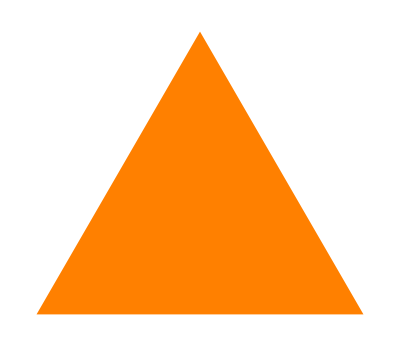

```mathematica
poly[n_]:=Graphics[{Orange,RegularPolygon[n]}];
poly[3]
```

```mathematica
Clear[f]
f[x_,y_]={y,x};
f[a,b]
```

{b,a}

```mathematica
Clear[f]
f[x_,y_]:=x y / (x+y);
f[4,5]
```

20/9

```mathematica
Clear[f]
f[x_,y_]:={x+y,x-y,x/y};
f[4,5]
```

{9,-1,4/5}

```mathematica
evenodd[x_]:=Which[x==0,Red,EvenQ[x],Black,OddQ[x],White];
evenodd[1]
evenodd[0]
evenodd[4]
```

GrayLevel[1]

RGBColor[1, 0, 0]

GrayLevel[0]

```mathematica
Clear[f]
f[x_,y_,z_]:=Which[x==1,y+z,x==2,y z,x==3,y^z];
f[1,9,5]
```

14

```mathematica
Clear[f]
f[n_]:=If[n==0||n== 1, 1, f[n-1]+f[n-2]];
f[1]
f[5]
```

1

8

```mathematica
animal[name_]:=EntityValue[Interpreter["Animal"][name],"Image"];
animal["Cat"]
```

-Graphics-

```mathematica
nearwords[String_,n_]:=Nearest[WordList[],String,n];
nearwords["cat",5]
```

{cat,at,bat,cab,cad}